```mathematica
SetDirectory[NotebookDirectory[]];
```

Phase line (Nf=2+1)

```mathematica
pb=Import["./pb-Nf2p1.dat"];
```

```mathematica
Tcdata=Import["./Tc.dat"];
```

```mathematica
lendata=Length[pb];
```

```mathematica
muBtoTlow=Table[{pb[[i,1]],pb[[i,2]]},{i,lendata}];
```

```mathematica
muBtoThigh=Table[{pb[[i,1]],pb[[i,3]]},{i,lendata}];
```

```mathematica
muBtoTc=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,lendata}];
```

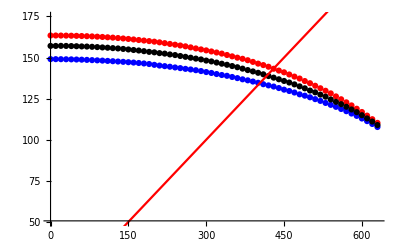

```mathematica
Show[ListPlot[muBtoThigh,PlotRange->{Automatic, {50,175}} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/3,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
TlowPoly[x_]=Fit[muBtoTlow,  {1,x^2,x^4},x];
```

```mathematica
ThighPoly[x_]=Fit[muBtoThigh, {1,x^2,x^4},x];
```

```mathematica
TcPoly[x_]=Fit[muBtoTc, {1,x^2,x^4},x];
```

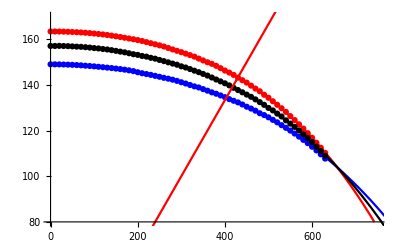

```mathematica
Show[Plot[ThighPoly[muB],{muB,0,750},PlotRange->{Automatic, {80,170}} ,PlotStyle->Red],Plot[TlowPoly[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPoly[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/3,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
FindRoot[ {TcPoly[x]== TlowPoly[x]},{x,600}]
```

{x→660.615}

```mathematica
FindRoot[ {TcPoly[x]== ThighPoly[x]},{x,600}]
```

{x→655.089}

```mathematica
FindRoot[ {TlowPoly[x]== ThighPoly[x]},{x,600}]
```

{x→657.645}

```mathematica
TcPoly[655.0893629284011]
```

104.547

muB/T=3

```mathematica
muBtoTlowR3=Table[{pb[[i,1]],pb[[i,2]]},{i,41}];
```

```mathematica
muBtoThighR3=Table[{pb[[i,1]],pb[[i,3]]},{i,44}];
```

```mathematica
muBtoTcR3=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,43}];
```

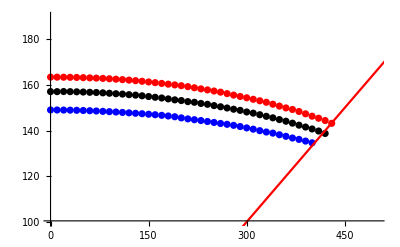

```mathematica
Show[ListPlot[muBtoThighR3,PlotRange->{{0,500}, {100,190}} ,PlotStyle->Red],ListPlot[muBtoTlowR3,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTcR3,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/3,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
TlowPolyR3[x_]=Fit[muBtoTlowR3,  {1,x^2,x^4},x];
```

```mathematica
ThighPolyR3[x_]=Fit[muBtoThighR3, {1,x^2,x^4},x];
```

```mathematica
TcPolyR3[x_]=Fit[muBtoTcR3, {1,x^2,x^4},x];
```

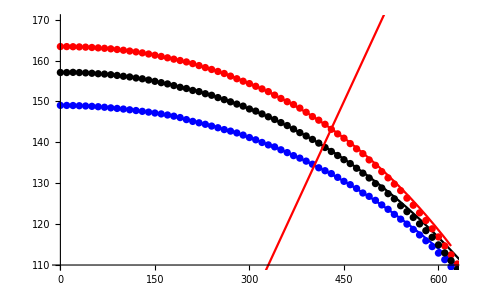

```mathematica
Show[Plot[ThighPolyR3[muB],{muB,0,620},PlotRange->{Automatic, {110,170}} ,PlotStyle->Red],Plot[TlowPolyR3[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPolyR3[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/3,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
d2TlowR3dT2[muB_]=D[TlowPolyR3[muB],{muB,2}];
```

```mathematica
d2TlowR3dT2[0]*TlowPolyR3[0]/(-2)
```

0.0125203

```mathematica
d2ThighR3dT2[muB_]=D[ThighPolyR3[muB],{muB,2}];
```

```mathematica
d2ThighR3dT2[0]*ThighPolyR3[0]/(-2)
```

0.0150747

```mathematica
d2TcR3dT2[muB_]=D[TcPolyR3[muB],{muB,2}];
```

```mathematica
d2TcR3dT2[0]*TcPolyR3[0]/(-2)
```

0.0148954

muB/T=4

```mathematica
muBtoTlowR4=Table[{pb[[i,1]],pb[[i,2]]},{i,51}];
```

```mathematica
muBtoThighR4=Table[{pb[[i,1]],pb[[i,3]]},{i,53}];
```

```mathematica
muBtoTcR4=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,52}];
```

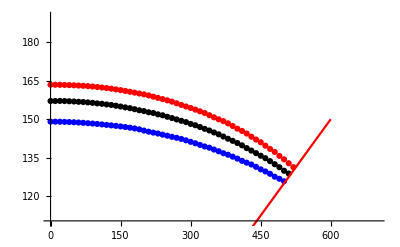

```mathematica
Show[ListPlot[muBtoThighR4,PlotRange->{{0,700}, {110,190}} ,PlotStyle->Red],ListPlot[muBtoTlowR4,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTcR4,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/4,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
TlowPolyR4[x_]=Fit[muBtoTlowR4,  {1,x^2,x^4},x];
```

```mathematica
ThighPolyR4[x_]=Fit[muBtoThighR4, {1,x^2,x^4},x];
```

```mathematica
TcPolyR4[x_]=Fit[muBtoTcR4, {1,x^2,x^4},x];
```

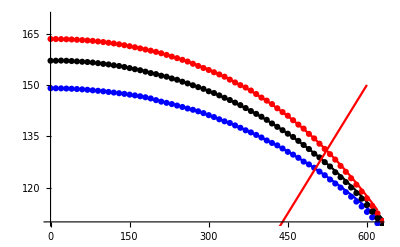

```mathematica
Show[Plot[ThighPolyR4[muB],{muB,0,620},PlotRange->{Automatic, {110,170}} ,PlotStyle->Red],Plot[TlowPolyR4[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPolyR4[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/4,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
d2TlowR4dT2[muB_]=D[TlowPolyR4[muB],{muB,2}];
```

```mathematica
d2TlowR4dT2[0]*TlowPolyR4[0]/(-2)
```

0.0125598

```mathematica
d2ThighR4dT2[muB_]=D[ThighPolyR4[muB],{muB,2}];
```

```mathematica
d2ThighR4dT2[0]*ThighPolyR4[0]/(-2)
```

0.0147352

```mathematica
d2TcR4dT2[muB_]=D[TcPolyR4[muB],{muB,2}];
```

```mathematica
d2TcR4dT2[0]*TcPolyR4[0]/(-2)
```

0.0146581

muB/T=2

```mathematica
muBtoTlowR2=Table[{pb[[i,1]],pb[[i,2]]},{i,29}];
```

```mathematica
muBtoThighR2=Table[{pb[[i,1]],pb[[i,3]]},{i,31}];
```

```mathematica
muBtoTcR2=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,30}];
```

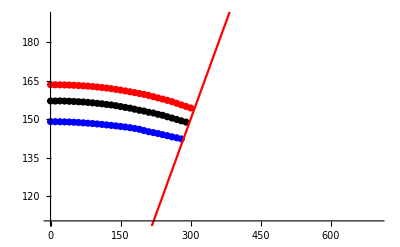

```mathematica
Show[ListPlot[muBtoThighR2,PlotRange->{{0,700}, {110,190}} ,PlotStyle->Red],ListPlot[muBtoTlowR2,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTcR2,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/2,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
TlowPolyR2[x_]=Fit[muBtoTlowR2,  {1,x^2,x^4},x];
```

```mathematica
ThighPolyR2[x_]=Fit[muBtoThighR2, {1,x^2,x^4},x];
```

```mathematica
TcPolyR2[x_]=Fit[muBtoTcR2, {1,x^2,x^4},x];
```

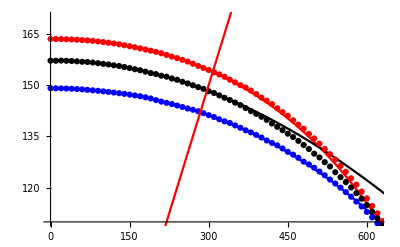

```mathematica
Show[Plot[ThighPolyR2[muB],{muB,0,620},PlotRange->{Automatic, {110,170}} ,PlotStyle->Red],Plot[TlowPolyR2[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPolyR2[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/2,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
d2TlowR2dT2[muB_]=D[TlowPolyR2[muB],{muB,2}];
```

```mathematica
d2TlowR2dT2[0]*TlowPolyR2[0]/(-2)
```

0.0124804

```mathematica
d2ThighR2dT2[muB_]=D[ThighPolyR2[muB],{muB,2}];
```

```mathematica
d2ThighR2dT2[0]*ThighPolyR2[0]/(-2)
```

0.014771

```mathematica
d2TcR2dT2[muB_]=D[TcPolyR2[muB],{muB,2}];
```

```mathematica
d2TcR2dT2[0]*TcPolyR2[0]/(-2)
```

0.0156405

```mathematica
k1=0.01564;
```

```mathematica
k2=0.01489;
```

```mathematica
(k1+k2)/2
```

0.015265

```mathematica
(k1-k2)/2
```

0.000375